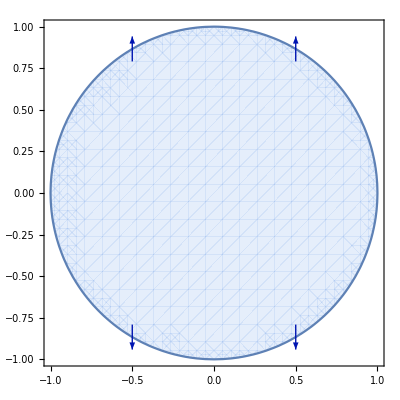

```mathematica
VectorPlot[{0,y},{x,-1,1},{y,-1,1},VectorPoints->2,RegionFunction->Function[{x,y},x^2+y^2≤1]]
```

```mathematica
points = {{-1,-1},{-1,1},{1,-1},{1,1},{0,1},{1,0},{-1,0},{0,-1}};
```

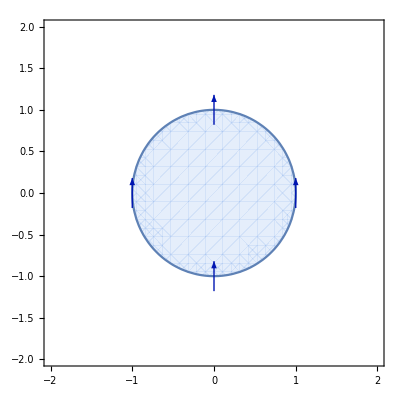

```mathematica
VectorPlot[{0,6},{x,-2,2},{y,-2,2},VectorPoints->points,RegionFunction->Function[{x,y},x^2+y^2≤1]]
```

```mathematica
H1={{A, -I*Subscript[B, 1]*(Subscript[k, x]-I*Subscript[k, y]), -I*(Subscript[B, 1]*Subscript[k, x]+I*Subscript[B, 2]*Subscript[k, y])}, {I*Subscript[B, 1]*(Subscript[k, x]+I*Subscript[k, y]), -A, 0}, {I*(Subscript[B, 1]*Subscript[k, x]-I*Subscript[B, 2]*Subscript[k, y]), 0, -A}}
```

{{A,-ⅈ B_1 (k_x-ⅈ k_y),-ⅈ (B_1 k_x+ⅈ B_2 k_y)},{ⅈ B_1 (k_x+ⅈ k_y),-A,0},{ⅈ (B_1 k_x-ⅈ B_2 k_y),0,-A}}

```mathematica
Eigenvalues[H1]
```

{-A,-√(A^2+2 B_1^2 k_x^2+B_1^2 k_y^2+B_2^2 k_y^2),√(A^2+2 B_1^2 k_x^2+B_1^2 k_y^2+B_2^2 k_y^2)}

```mathematica
Eigenvectors[H1]
```

{{0,-(B_1 k_x+ⅈ B_2 k_y)/(B_1 (k_x-ⅈ k_y)),1},{(ⅈ (-A+√(A^2+2 B_1^2 k_x^2+B_1^2 k_y^2+B_2^2 k_y^2)))/(B_1 k_x-ⅈ B_2 k_y),-(-B_1 k_x-ⅈ B_1 k_y)/(B_1 k_x-ⅈ B_2 k_y),1},{-(ⅈ (A+√(A^2+2 B_1^2 k_x^2+B_1^2 k_y^2+B_2^2 k_y^2)))/(B_1 k_x-ⅈ B_2 k_y),-(-B_1 k_x-ⅈ B_1 k_y)/(B_1 k_x-ⅈ B_2 k_y),1}}